# PME3380 - Rec

## Posições e velocidades

```mathematica
x1[t] = -x0[t]+(L1/2)*Sin[alpha[t]];
y1[t] = -(L1/2)*Cos[alpha[t]];

x2[t] = -x0[t]+L1*Sin[alpha[t]] + (L2/2)*Sin[beta[t]];
y2[t] = -L1*Cos[alpha[t]]- (L2/2)*Cos[beta[t]];

x3[t] = -x0[t]+L1*Sin[alpha[t]] + L2*Sin[beta[t]];
y3[t] =-L1*Cos[alpha[t]]- L2*Cos[beta[t]];

x1'[t]=D[x1[t],t];
y1'[t]=D[y1[t],t];
x2'[t]=D[x2[t],t];
y2'[t]=D[y2[t],t];
x3'[t] =D[x3[t],t];
y3'[t]=D[y3[t],t];


v1[t]=Sqrt[x1'[t]^2+y1'[t]^2];
v2[t]=Sqrt[x2'[t]^2+y2'[t]^2];
v3[t]=Sqrt[x3'[t]^2+y3'[t]^2];
```

## Energia cinética

```mathematica
IG1 = (m1*L1^2)/12;
IG2 = (m2*L2^2)/12;
IG3 = (m3*L3^2)/12;
T1=1/2 m1*v1[t]^2+1/2*IG1*(alpha'[t])^2;
T2=1/2 m2*v2[t]^2+1/2*IG2*(beta'[t])^2;
T3=1/2 m3*v3[t]^2+ 1/2*IG3*(beta'[t])^2; 
T=T1+T2 + T3
```

1/24 L1^2 m1 alpha'[t]^2+1/24 L2^2 m2 beta'[t]^2+1/24 L3^2 m3 beta'[t]^2+1/2 m1 (1/4 L1^2 Sin[alpha[t]]^2 alpha'[t]^2+(1/2 L1 Cos[alpha[t]] alpha'[t]-x0'[t])^2)+1/2 m2 ((L1 Sin[alpha[t]] alpha'[t]+1/2 L2 Sin[beta[t]] beta'[t])^2+(L1 Cos[alpha[t]] alpha'[t]+1/2 L2 Cos[beta[t]] beta'[t]-x0'[t])^2)+1/2 m3 ((L1 Sin[alpha[t]] alpha'[t]+L2 Sin[beta[t]] beta'[t])^2+(L1 Cos[alpha[t]] alpha'[t]+L2 Cos[beta[t]] beta'[t]-x0'[t])^2)

## Energia potencial

```mathematica
V1=m1*g*y1[t];
V2=m2*g*y2[t];
V3=m3*g*y3[t];
V=V1+V2+V3
```

-1/2 g L1 m1 Cos[alpha[t]]+g m3 (-L1 Cos[alpha[t]]-L2 Cos[beta[t]])+g m2 (-L1 Cos[alpha[t]]-1/2 L2 Cos[beta[t]])

## Lagrange

```mathematica
L=T-V;
```

## Rayleigh

```mathematica
R= 1/2*c*(alpha'[t]-beta'[t])^2;
```

## Equações

```mathematica
eq1=Simplify[D[D[L,alpha'[t]],t]-D[L,alpha[t]]+ D[R,alpha'[t]]] (*Para alpha*)

eq2=Simplify[D[D[L,beta'[t]],t]-D[L,beta[t]] + D[R,beta'[t]]](*Para beta*)

eq3=Simplify[D[D[L,x0'[t]],t]-D[L,x0[t]]](*Para x0*)
```

c alpha'[t]+1/6 (-6 c beta'[t]+3 L1 L2 (m2+2 m3) Sin[alpha[t]-beta[t]] beta'[t]^2+L1 (2 L1 (m1+3 (m2+m3)) alpha''[t]+3 (L2 (m2+2 m3) Cos[alpha[t]-beta[t]] beta''[t]+(m1+2 (m2+m3)) (g Sin[alpha[t]]-Cos[alpha[t]] x0''[t]))))

1/2 g L2 m2 Sin[beta[t]]+g L2 m3 Sin[beta[t]]-c alpha'[t]-1/2 L1 L2 (m2+2 m3) Sin[alpha[t]-beta[t]] alpha'[t]^2+c beta'[t]+1/2 L1 L2 m2 Cos[alpha[t]-beta[t]] alpha''[t]+L1 L2 m3 Cos[alpha[t]-beta[t]] alpha''[t]+1/3 L2^2 m2 beta''[t]+L2^2 m3 beta''[t]+1/12 L3^2 m3 beta''[t]-1/2 L2 m2 Cos[beta[t]] x0''[t]-L2 m3 Cos[beta[t]] x0''[t]

1/2 (L1 (m1+2 (m2+m3)) Sin[alpha[t]] alpha'[t]^2+L2 (m2+2 m3) Sin[beta[t]] beta'[t]^2-L1 m1 Cos[alpha[t]] alpha''[t]-2 L1 m2 Cos[alpha[t]] alpha''[t]-2 L1 m3 Cos[alpha[t]] alpha''[t]-L2 m2 Cos[beta[t]] beta''[t]-2 L2 m3 Cos[beta[t]] beta''[t]+2 m1 x0''[t]+2 m2 x0''[t]+2 m3 x0''[t])

## Equações finais separadas

```mathematica
EL = {eq1 == 0,eq2 ==0, eq3==F};
Subs1={alpha[t]->Subscript[x, 1], beta[t]->Subscript[x, 2],x0[t]->Subscript[x, 3],alpha'[t]->Subscript[x, 4],beta'[t]->Subscript[x, 5],x0'[t]->Subscript[x, 6],F[t]->F};
ELnl=EL/.Subs1;
PPnl=Simplify[Solve[ELnl,{alpha''[t],beta''[t],x0''[t]}]]//First;

𝕩[t]={Subscript[x, 1][t],Subscript[x, 2][t],Subscript[x, 3][t],Subscript[x, 4][t],Subscript[x, 5][t],Subscript[x, 6][t]};
𝕩'[t]={Subscript[x, 4][t],Subscript[x, 5][t],Subscript[x, 6][t],alpha''[t],beta''[t],x0''[t]};
EENL={D[𝕩[t],t]==𝕩'[t]/.PPnl[[1]]/.PPnl[[2]]/.PPnl[[3]]};
TableForm[EENL]
```

{x_1'[t],x_2'[t],x_3'[t],x_4'[t],x_5'[t],x_6'[t]}=={x_4[t],x_5[t],x_6[t],-(96 ((-1/12 (m1+m2+m3) (L3^2 m3+4 L2^2 (m2+3 m3))+1/4 L2^2 (m2+2 m3)^2 Cos[x_2]^2) (-1/4 L1 (m1+2 (m2+m3)) Cos[x_1] (-g L2 (m2+2 m3) Sin[x_2]+2 c x_4+L1 L2 (m2+2 m3) Sin[x_1-x_2] x_4^2-2 c x_5)-1/4 L2 (m2+2 m3) Cos[x_2] (g L1 (m1+2 (m2+m3)) Sin[x_1]+2 c x_4-2 c x_5+L1 L2 (m2+2 m3) Sin[x_1-x_2] x_5^2))-1/24 L1 ((m1+2 (m2+m3)) (L3^2 m3+4 L2^2 (m2+3 m3)) Cos[x_1]-6 L2^2 (m2+2 m3)^2 Cos[x_1-x_2] Cos[x_2]) (-1/2 (m1+m2+m3) (g L2 (m2+2 m3) Sin[x_2]-2 c x_4-L1 L2 (m2+2 m3) Sin[x_1-x_2] x_4^2+2 c x_5)-1/4 L2 (m2+2 m3) Cos[x_2] (-2 F+L1 (m1+2 (m2+m3)) Sin[x_1] x_4^2+L2 (m2+2 m3) Sin[x_2] x_5^2))))/(L1^2 L2 (m2+2 m3) (4 (3 (m1+2 (m2+m3)) Cos[2 x_1-x_2]-(m1+6 (m2+m3)) Cos[x_2]) (-1/12 (m1+m2+m3) (L3^2 m3+4 L2^2 (m2+3 m3))+1/4 L2^2 (m2+2 m3)^2 Cos[x_2]^2)+((L3^2 m3 (m1+2 (m2+m3))+L2^2 (5 m2^2+20 m2 m3+12 m3^2+4 m1 (m2+3 m3))) Cos[x_1]-3 L2^2 (m2+2 m3)^2 Cos[x_1-2 x_2]) (m1 Cos[x_1] Cos[x_2]+2 (m1+m2+m3) Sin[x_1] Sin[x_2]))),-(2 (3 L1 L2 (m2+2 m3) (6 F (m1+2 (m2+m3)) Cos[2 x_1-x_2]-2 F (m1+6 (m2+m3)) Cos[x_2]-g m1 (3 (m1+2 (m2+m3)) Sin[2 x_1-x_2]+(m1-2 (m2+m3)) Sin[x_2]))+6 c (-5 L1 m1^2-20 L1 m1 m2-12 L1 m2^2-20 L1 m1 m3-24 L1 m2 m3-12 L1 m3^2+3 L1 (m1+2 (m2+m3))^2 Cos[2 x_1]-6 L2 m1 (m2+2 m3) Cos[x_1] Cos[x_2]-12 L2 m1 m2 Sin[x_1] Sin[x_2]-12 L2 m2^2 Sin[x_1] Sin[x_2]-24 L2 m1 m3 Sin[x_1] Sin[x_2]-36 L2 m2 m3 Sin[x_1] Sin[x_2]-24 L2 m3^2 Sin[x_1] Sin[x_2]) x_4-3 L1^2 L2 m1 (m2+2 m3) (4 (m1+3 (m2+m3)) Cos[x_2] Sin[x_1]-2 (m1+4 (m2+m3)) Cos[x_1] Sin[x_2]) x_4^2-6 c (-5 L1 m1^2-20 L1 m1 m2-12 L1 m2^2-20 L1 m1 m3-24 L1 m2 m3-12 L1 m3^2+3 L1 (m1+2 (m2+m3))^2 Cos[2 x_1]-6 L2 m1 (m2+2 m3) Cos[x_1] Cos[x_2]-12 L2 m1 m2 Sin[x_1] Sin[x_2]-12 L2 m2^2 Sin[x_1] Sin[x_2]-24 L2 m1 m3 Sin[x_1] Sin[x_2]-36 L2 m2 m3 Sin[x_1] Sin[x_2]-24 L2 m3^2 Sin[x_1] Sin[x_2]) x_5-3 L1 L2^2 m1 (m2+2 m3)^2 (3 Sin[2 (x_1-x_2)]+Sin[2 x_2]) x_5^2))/(L1 (20 L2^2 m1^2 m2+50 L2^2 m1 m2^2+12 L2^2 m2^3+60 L2^2 m1^2 m3+5 L3^2 m1^2 m3+200 L2^2 m1 m2 m3+20 L3^2 m1 m2 m3+60 L2^2 m2^2 m3+12 L3^2 m2^2 m3+120 L2^2 m1 m3^2+20 L3^2 m1 m3^2+48 L2^2 m2 m3^2+24 L3^2 m2 m3^2+12 L3^2 m3^3-3 (m1+2 (m2+m3)) (L3^2 m3 (m1+2 (m2+m3))+2 L2^2 (2 m1 (m2+3 m3)+m2 (m2+4 m3))) Cos[2 x_1]-18 L2^2 m1 (m2+2 m3)^2 Cos[2 (x_1-x_2)]+6 L2^2 m1 m2^2 Cos[2 x_2]+24 L2^2 m1 m2 m3 Cos[2 x_2]+24 L2^2 m1 m3^2 Cos[2 x_2])),-(L1 (36 F L2^2 (m2+2 m3)^2 Cos[2 (x_1-x_2)]+3 g (m1+2 (m2+m3)) (L3^2 m3 (m1+2 (m2+m3))+2 L2^2 (2 m1 (m2+3 m3)+m2 (m2+4 m3))) Sin[2 x_1]-2 (4 F L3^2 m3 (m1+3 (m2+m3))+2 F L2^2 (15 m2^2+60 m2 m3+36 m3^2+8 m1 (m2+3 m3))+3 g L2^2 m1 (m2+2 m3)^2 Sin[2 x_2]))+12 c ((L3^2 m3 (m1+2 (m2+m3))+L2^2 (5 m2^2+20 m2 m3+12 m3^2+4 m1 (m2+3 m3))) Cos[x_1]-L2 (m2+2 m3) (3 L2 (m2+2 m3) Cos[x_1-2 x_2]-3 L1 (m1+2 (m2+m3)) Cos[2 x_1-x_2]+L1 (m1+6 (m2+m3)) Cos[x_2])) x_4+2 L1^2 ((2 L3^2 m3 (m1^2+5 m1 (m2+m3)+6 (m2+m3)^2)+L2^2 (8 m1^2 (m2+3 m3)+12 m2 (m2^2+5 m2 m3+4 m3^2)+5 m1 (5 m2^2+20 m2 m3+12 m3^2))) Sin[x_1]+3 L2^2 m1 (m2+2 m3)^2 Sin[x_1-2 x_2]) x_4^2-12 c ((L3^2 m3 (m1+2 (m2+m3))+L2^2 (5 m2^2+20 m2 m3+12 m3^2+4 m1 (m2+3 m3))) Cos[x_1]-L2 (m2+2 m3) (3 L2 (m2+2 m3) Cos[x_1-2 x_2]-3 L1 (m1+2 (m2+m3)) Cos[2 x_1-x_2]+L1 (m1+6 (m2+m3)) Cos[x_2])) x_5+L1 L2 (m2+2 m3) (3 (L3^2 m3 (m1+2 (m2+m3))+2 L2^2 (2 m1 (m2+3 m3)+m2 (m2+4 m3))) Sin[2 x_1-x_2]+(L3^2 m3 (m1+6 (m2+m3))+2 L2^2 (2 m1 (m2+3 m3)+3 m2 (m2+4 m3))) Sin[x_2]) x_5^2)/(L1 (20 L2^2 m1^2 m2+50 L2^2 m1 m2^2+12 L2^2 m2^3+60 L2^2 m1^2 m3+5 L3^2 m1^2 m3+200 L2^2 m1 m2 m3+20 L3^2 m1 m2 m3+60 L2^2 m2^2 m3+12 L3^2 m2^2 m3+120 L2^2 m1 m3^2+20 L3^2 m1 m3^2+48 L2^2 m2 m3^2+24 L3^2 m2 m3^2+12 L3^2 m3^3-3 (m1+2 (m2+m3)) (L3^2 m3 (m1+2 (m2+m3))+2 L2^2 (2 m1 (m2+3 m3)+m2 (m2+4 m3))) Cos[2 x_1]-18 L2^2 m1 (m2+2 m3)^2 Cos[2 (x_1-x_2)]+6 L2^2 m1 m2^2 Cos[2 x_2]+24 L2^2 m1 m2 m3 Cos[2 x_2]+24 L2^2 m1 m3^2 Cos[2 x_2]))}

## Matrizes

```mathematica
EQ4=
Simplify[𝕩'[t][[4]]/.PPnl[[1]]/.PPnl[[2]]/.PPnl[[3]]];


EQ5=
Simplify[𝕩'[t][[5]]/.PPnl[[1]]/.PPnl[[2]]/.PPnl[[3]]];


EQ6=
Simplify[𝕩'[t][[6]]/.PPnl[[1]]/.PPnl[[2]]/.PPnl[[3]]];



A41=D[EQ4,Subscript[x, 1]];
A42=D[EQ4,Subscript[x, 2]];
A43=D[EQ4,Subscript[x, 3]];
A44=D[EQ4,Subscript[x, 4]];
A45=D[EQ4,Subscript[x, 5]];
A46=D[EQ4,Subscript[x, 6]];

A51=D[EQ5,Subscript[x, 1]];
A52=D[EQ5,Subscript[x, 2]];
A53=D[EQ5,Subscript[x, 3]];
A54=D[EQ5,Subscript[x, 4]];
A55=D[EQ5,Subscript[x, 5]];
A56=D[EQ5,Subscript[x, 6]];

A61=D[EQ6,Subscript[x, 1]];
A62=D[EQ6,Subscript[x, 2]];
A63=D[EQ6,Subscript[x, 3]];
A64=D[EQ6,Subscript[x, 4]];
A65=D[EQ6,Subscript[x, 5]];
A66=D[EQ6,Subscript[x, 6]];

B11=0;
B21=0;
B31=0;
B41=D[EQ4,F];
B51=D[EQ5,F];
B61=D[EQ6,F];

SubAll={m1->3,m2->0.4,m3->60,g->9.81,L1->0.25,L2->0.65,L3->1.2,c->1,F-> 80UnitStep[1-t],Subscript[x, 1]->0,Subscript[x, 2]->0,Subscript[x, 3]->0,Subscript[x, 4]->0,Subscript[x, 5]->0,Subscript[x, 6]->0 };

A11n= A12n=A13n=A15n=A16n=A21n=A22n=A23n=A24n=A26n =A31n=A32n=A33n= A34n=A35n= 0;
A14n = A25n=A36n=1;

A41n=A41/.SubAll;
A42n=A42/.SubAll;
A43n=A43/.SubAll;
A44n=A44/.SubAll;
A45n=A45/.SubAll;
A46n=A46/.SubAll;

A51n=A51/.SubAll;
A52n=A52/.SubAll;
A53n=A53/.SubAll;
A54n=A54/.SubAll;
A55n=A55/.SubAll;
A56n=A56/.SubAll;

A61n=A61/.SubAll;
A62n=A62/.SubAll;
A63n=A63/.SubAll;
A64n=A64/.SubAll;
A65n=A65/.SubAll;
A66n=A66/.SubAll;

B11n=0;
B21n=0;
B31n=0;
B41n=B41/.SubAll;
B51n=B51/.SubAll;
B61n=B61/.SubAll;
```

```mathematica
A={{A11n,A12n,A13n, A14n,A15n,A16n},
{A21n,A22n,A23n,A24n,A25n,A26n},
{A31n,A32n,A33n, A34n,A35n,A36n},
{A41n,A42n,A43n, A44n,A45n,A46n},
{A51n,A52n,A53n, A54n,A55n,A56n},
{A61n,A62n,A63n, A64n,A65n,A66n}};
MatrixForm[A]
```

(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
-2814.07 | 194.77 | 0 | -19.0442 | 19.0442 | 0
77.0268 | -50.729 | 0 | 0.639544 | -0.639544 | 0
-639.332 | 16.2308 | 0 | -4.25368 | 4.25368 | 0)

```mathematica
B={{B11n},
{B21n},
{B31n},
{B41n},
{B51n},
{B61n}};
MatrixForm[B]
```

(0
0
0
4.2114
-0.0422826
1.01762)

```mathematica
𝒞 ={{1,0,0, 0,0,0},
{0,1,0,0,0,0},
{0,0,1, 0,0,0}};

𝒟={{0},
{0},
{0}};
```

## Polinômio característico

```mathematica
Poli=CharacteristicPolynomial[A,s];
TraditionalForm[Poli]
```

s^6+19.6837 s^5+2864.8 s^4+1174.34 s^3+127752. s^2

## Polos

```mathematica
Polos=TraditionalForm[TableForm[Solve[Poli==0]]]/.{s->Subscript[s, P]}
```

s_P→-9.79104+52.1689 ⅈ
s_P→-9.79104-52.1689 ⅈ
s_P→-0.0508301+6.73354 ⅈ
s_P→-0.0508301-6.73354 ⅈ
s_P→0.
s_P→0.

## Função de Transferência

```mathematica
G =𝒞.Inverse[s*IdentityMatrix[6]-A].B+𝒟;
MatrixForm[G]
```

(0.-(0.0422826 (194.77 s^2+19.0442 s^3))/(127752. s^2+1174.34 s^3+2864.8 s^4+19.6837 s^5+s^6)+(4.2114 (50.729 s^2+0.639544 s^3+s^4))/(127752. s^2+1174.34 s^3+2864.8 s^4+19.6837 s^5+s^6)
0.+(4.2114 (77.0268 s^2+0.639544 s^3))/(127752. s^2+1174.34 s^3+2864.8 s^4+19.6837 s^5+s^6)-(0.0422826 (2814.07 s^2+19.0442 s^3+s^4))/(127752. s^2+1174.34 s^3+2864.8 s^4+19.6837 s^5+s^6)
(4.2114 (-31182.5-286.638 s-639.332 s^2-4.25368 s^3))/(127752. s^2+1174.34 s^3+2864.8 s^4+19.6837 s^5+s^6)-(0.0422826 (-78847.8-724.791 s+16.2308 s^2+4.25368 s^3))/(127752. s^2+1174.34 s^3+2864.8 s^4+19.6837 s^5+s^6)+(1.01762 (127752.+1174.34 s+2864.8 s^2+19.6837 s^3+s^4))/(127752. s^2+1174.34 s^3+2864.8 s^4+19.6837 s^5+s^6))

## Graficos das Posicoes

```mathematica
ELn2=EL;
PPn2=Simplify[Solve[ELn2,{alpha''[t],beta''[t],x0''[t]}]]//First;
W'[t]={Subscript[x, 4][t],Subscript[x, 5][t],Subscript[x, 6][t],alpha''[t],beta''[t],x0''[t]}
```

{x_4[t],x_5[t],x_6[t],alpha''[t],beta''[t],x0''[t]}

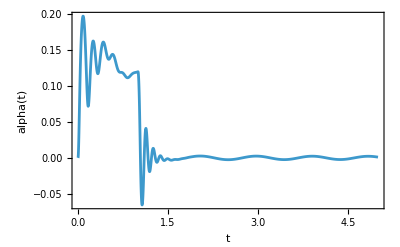

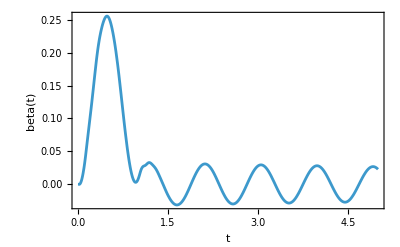

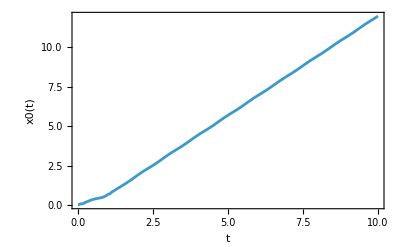

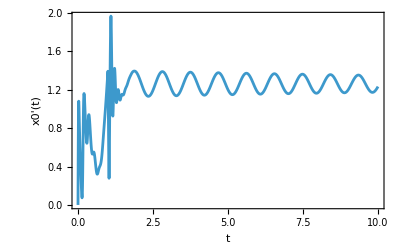

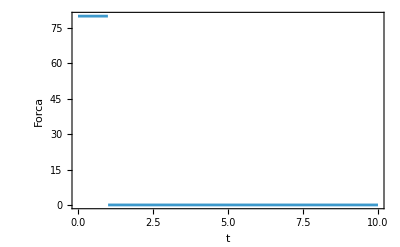

```mathematica
eqalpha=Simplify[W'[t][[4]]/.PPn2[[1]]/.PPn2[[2]]/.PPn2[[3]]];
eqbeta=Simplify[W'[t][[5]]/.PPn2[[1]]/.PPn2[[2]]/.PPn2[[3]]];
eqx0=Simplify[W'[t][[6]]/.PPn2[[1]]/.PPn2[[2]]/.PPn2[[3]]];

m1= 3;
m2=0.4;
m3=60;
g=9.81;
L1=0.25;
L2=0.65;
L3=1.2;
c=1;
F =80UnitStep[1-t];
tend =600;
NumSolution=NDSolve[{alpha''[t]==eqalpha,beta''[t]==eqbeta,x0''[t]==eqx0,alpha[0]==0,alpha'[0]==0,beta[0]==0,beta'[0]==0,x0[0]==0,x0'[0]==0},{alpha,beta,x0},{t,0,tend}];


Plot[Evaluate[alpha[t]/.NumSolution],{t,0,5},FrameLabel->{t,alpha[t]},DisplayFunction->Identity,Axes->False,Frame->True,PlotRange->All]

Plot[Evaluate[beta[t]/.NumSolution],{t,0,5},FrameLabel->{t,beta[t]},DisplayFunction->Identity,Axes->False,Frame->True,PlotRange->All]

Plot[Evaluate[x0[t]/.NumSolution],{t,0,10},FrameLabel->{t,x0[t]},DisplayFunction->Identity,Axes->False,Frame->True,PlotRange->All]

Plot[Evaluate[x0'[t]/.NumSolution],{t,0,10},FrameLabel->{t,x0'[t]},DisplayFunction->Identity,Axes->False,Frame->True,PlotRange->All]

Plot[F,{t,0,10},FrameLabel->{t,Forca},DisplayFunction->Identity,Axes->False,Frame->True,PlotRange->All]
```

```mathematica
Quit
```